Системы аналитических вычислений.

Лабораторная работа №4.

Студент: Короткевич Л. В., М8О-208Б-19

```mathematica
tasks = {
    Sin[2*x^3]^2/x^3
    , (x^2 - 4)*Sin[(Pi*(x^2))/6] / (x^2 - 1)
    , Sqrt[Abs[3*x^3 + 2*x^2 - 10*x]] / (4*x)
    , 1/2 * Log[Sqrt[x^2 + 1] / Sqrt[x^2 - 1]] - 15*x^2
    , (x^3 - x^2 - x + 1)^(1/3) / Tan[x]
    , 2*Log[(x - 1) / x] + 1
    , Log[x - 1] / (x - 1)^2
};
```

```mathematica
getVariantForNumber[number_, variationsQuo_]:=(
    Module[{t},
        t = Mod[number , variationsQuo];
        If[t ≠ 0
                , t
                , variationsQuo
            ]
    ]
)
```

```mathematica
Table[Plot[tasks[[i]], {x, -10, 10}], {i, 1, Length[tasks]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
yourNumber = 15;
numberOfYourTask = getVariantForNumber[yourNumber, Length[tasks]];
Print["Number of your task: ", numberOfYourTask]
```

Number of your task: 1

График

```mathematica
f[y_] := tasks[[numberOfYourTask]]/.x->y;
```

```mathematica
Plot[f[x], {x, 0, 7}, PlotRange->{-0.5,0.5}]
```

-Graphics-

Область определения

```mathematica
D:x≠1
```

D:x≠1

Проверка на чётность/нечётность

```mathematica
even = TautologyQ[f[x] == f[-x]];
noteven = TautologyQ[f[x] + f[-x] == 0];
```

```mathematica
If[even == True,"Функция четная", Null]
If[noteven == True,"Функция нечетная", Null]
If[Not[even||noteven], "Функция прочая", Null]
```

Функция нечетная

Проверка на переодичность

```mathematica
Solve[f[x+T] == f[x], T]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(Sin[2 (T+x)^3]^2)/(T+x)^3==(Sin[2 x^3]^2)/x^3,T]

f[x+T] != f[x], следовательно функция не является периодической.

Точки пересечения с осями координат:
с осью Y их нет в силу одз, а с осью X - бесконечно много

```mathematica
sols = Solve[f[x] == 0 && x > 0 && x < 2, x];
points = {x, 0} /. sols;
```

```mathematica
g1 = Plot[f[x], {x, 0, 7}, PlotRange->{-0.5,0.5}];
g2 = ListPlot[points, PlotStyle->{Black, PointSize[Large]}];
Show[{g1, g2}]
```

-Graphics-

Промежутуки знакопостоянства

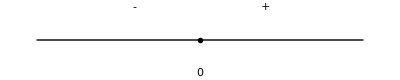

```mathematica
Show[
    Graphics[Line[{{-5, 0}, {5, 0}}]],
    Graphics[{PointSize[0.01], Point[{0, 0}, VertexColors->Blue]}],
    Graphics[Text[0, {0, -0.3}]],
    Graphics[Text[Style["-", FontSize -> Scaled[0.05]], {-2, 0.3}]],
    Graphics[Text[Style["+", FontSize -> Scaled[0.05]], {2, 0.3}]]
]
```

Промежутки возрастания и убывания

```mathematica
df = D[f[x], x]
```

(12 Cos[2 x^3] Sin[2 x^3])/x-(3 Sin[2 x^3]^2)/x^4

```mathematica
Solve[df == 0, x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(12 Cos[2 x^3] Sin[2 x^3])/x-(3 Sin[2 x^3]^2)/x^4==0,x]

Функция имеет бесконечное число промежутков возрастания и убывания, экстремумов. Решить аналитически это невозможно.

```mathematica
Reduce[df > 0 && x > 0 && x < 1, x]
```

0<x<Root0.835Root[{-2 #1^3+Tan[#1^3]+2 #1^3 Tan[#1^3]^2&,0.83528566252624430972557}]0.8352856625262443

Можно лишь таким, наивным образом, в частном случае заключить, что на [0; 0.83] функция будет  возрастать.

```mathematica
Reduce[df < 0 && x > 0 && x < 1.2, x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.835286<x<1.16245

... а убывать функция будет от 0,83 до 1,16, например.

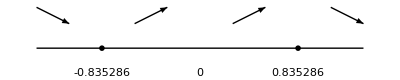

```mathematica
Show[
    Graphics[Line[{{-5, 0}, {5, 0}}]],
    Graphics[Text[-0.835286, {-3, -0.3}]],
    Graphics[{PointSize[0.01], Point[{-3, 0}, VertexColors->Blue]}],
    Graphics[Text[0, {0, -0.3}]],
    Graphics[{PointSize[0.01], Point[{3, 0}, VertexColors->Blue]}],
    Graphics[Text[0.835286, {3, -0.3}]],
    Graphics[Arrow[{{4, 0.5}, {5, 0.3}}]],
    Graphics[Arrow[{{1, 0.3}, {2, 0.5}}]],
    Graphics[Arrow[{{-2, 0.3}, {-1, 0.5}}]],
    Graphics[Arrow[{{-5, 0.5}, {-4, 0.3}}]]
]
```

Точки экстремума и значения в этих точках:

Как несложно догадаться, +-0.83 -- точки локального экстремума. Значения в них:

```mathematica
f[0.83]
f[-0.83]
```

1.44865

-1.44865

Непрерывность. Наличие точек разрыва и их классификация

Наша функция непрерывна на . А в точке  левосторонний и правосторонний пределы равны: это точка устранимого разрыва. Покажем это.

```mathematica
Limit[f[x], x->0]
```

0

```mathematica
Limit[f[x], x->-0]
```

0

Асимптоты
определим k, b классическим образом:

```mathematica
Limit[Sin[2*x^3]^2/x^4, x->+∞]
```

0

```mathematica
Limit[Sin[2*x^3]^2/x^3, x->+∞]
```

0

Получаем уравнение горизонтальной асимптоты: y = 0.

А вертикальная асимптота, как нетрудно догадаться: x = 0. Это мы установили, когда считали пределы в точке 0.